```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
customMultivariateT[mu_,aSigma_,ν_]:=Module[{aSigmaAdjusted = aSigma * ((ν-2)/ν)},MultivariateTDistribution[mu,aSigmaAdjusted,ν]]
```

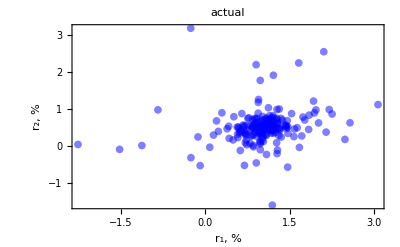

```mathematica
sigma = {{2,0.2},{0.2,1}};
μ = {1,0.5};
data = RandomVariate[customMultivariateT[μ,sigma,2.1],{200}];
ListPlot[data,PlotStyle->Opacity[0.5,Blue],Frame->{True,True,False,False},Axes->False,FrameLabel->{"r_1, %","r_2, %"},BaseStyle->{FontSize->18},FrameTicks->Automatic,PlotLabel->"actual",PlotRange->Full]
```

```mathematica
Clear[μ1,μ2]
aNormResults=FindDistributionParameters[data,MultinormalDistribution[{μ1,μ2},{{a,b},{b,c}}]];
μ1N= aNormResults[[1,2]];
μ2N= aNormResults[[2,2]];
a1=aNormResults[[3,2]];
b1=aNormResults[[4,2]];
c1=aNormResults[[5,2]];
aSigmaEstN = {{a1,b1},{b1,c1}};
μEstN  = {μ1N,μ1N};
```

```mathematica
aTResults =FindDistributionParameters[data,MultivariateTDistribution[{μ1,μ2},{{a,b},{b,c}},1]];
μ1T = aTResults[[1,2]];
μ2T= aTResults[[2,2]];
a1=aTResults[[3,2]];
b1=aTResults[[5,2]];
c1=aTResults[[4,2]];
aSigmaEstT = {{a1,b1},{b1,c1}};
μEstT  = {μ1T,μ1T};
```

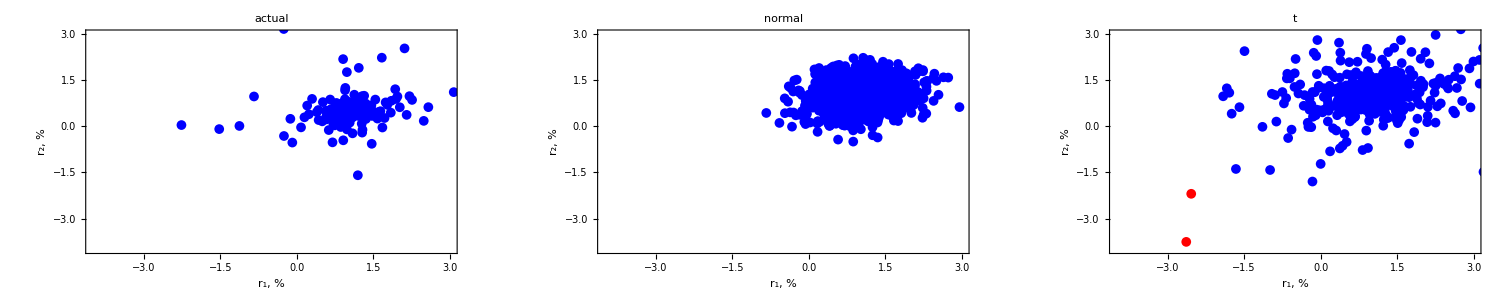

```mathematica
aRange = {{-4,3},{-4,3}};
bRange = aRange;
dataT = RandomVariate[MultivariateTDistribution[μEstT,aSigmaEstT,1],{1000}];
dataN = RandomVariate[MultinormalDistribution[μEstN,aSigmaEstN],{1000}];
dataTRed = Cases[(If[And[#[[1]]<-2,#[[2]]<-2],#,{}]&/@dataT),{_,_}];
dataTBlue= Cases[(If[And[#[[1]]>-2,#[[2]]>-2],#,{}]&/@dataT),{_,_}];
g1=ListPlot[data,PlotStyle->Blue,Frame->{True,True,False,False},Axes->False,FrameLabel->{"r_1, %","r_2, %"},BaseStyle->{FontSize->18},FrameTicks->Automatic,PlotLabel->"actual",PlotRange->aRange,PlotMarkers->{●,10}];
g2=ListPlot[dataN,Frame->{True,True,False,False},Axes->False,FrameLabel->{"r_1, %","r_2, %"},BaseStyle->{FontSize->18},FrameTicks->Automatic,PlotStyle->Blue,PlotLabel->"normal",PlotRange->bRange,PlotMarkers->{●,10}];
g3=ListPlot[{dataTBlue,dataTRed},Frame->{True,True,False,False},Axes->False,FrameLabel->{"r_1, %","r_2, %"},BaseStyle->{FontSize->18},FrameTicks->Automatic,PlotLabel->"t",PlotRange->bRange,PlotStyle->{Blue,Red},PlotMarkers->{{●,10},{●,10}}];
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1500]
```